```mathematica
numberOfAgents = 100;
donationCost = -10;
buyCost = -40;
donationHealthChange=7;
usageUtil = 5;
waitCost = -1;
fullToolHealth=10;

agentParams = Array[Function[x,
{(*RandomReal[0.4], (* How often a tool is needed *)*)
1,
RandomReal[0.05], (* Prob to buy tool *)
RandomReal[0.2], (* Prob to donate *)
0, (* Has tool (tool health) *)
0 (* payoff *)
}],numberOfAgents];
```

Calculate payoff now has a max number of tools so that a player that donates doesn’t have to if the pool is full.

```mathematica
(* Returns the utility, the updated agent, and change in poolHealth.
int, agent, int *)
CalculatePayoff[agent_,nPTools_,maxPTools_]:=Module[
{p=agent[[1]],pb=agent[[2]],
pd=agent[[3]],toolHealth=agent[[4]],
util=agent[[5]],poolHealthChange=0},
If[RandomReal[]<p,
If[toolHealth>0,
util+=usageUtil; toolHealth-=1,
If[RandomReal[]<pb,
toolHealth=fullToolHealth;
util+=buyCost+usageUtil,
If[nPTools>0,
util+=usageUtil;poolHealthChange-=1,
util+=waitCost]
]
],
If[RandomReal[]<pd &&maxPTools<=nPTools,
poolHealthChange+=donationHealthChange;
util+=donationCost,
util+=0
]
];
{{p,pb,pd,toolHealth,util},poolHealthChange}
];

CalculatePayoff[{0,0,1,5,0},3]
```

CalculatePayoff[{0,0,1,5,0},3]

```mathematica
MutateValue[v_] := Module[{value},
If[v>0.5,distance = 1-v,distance =v];
value=RandomVariate[NormalDistribution[v,(*distance/4)+*)0.1]];
If[value<=0,0,Min[value,1]]
];
MutateValue[0.1]
MutateAgent[agent_]:=Module[
{p=agent[[1]],pb=agent[[2]],pd=agent[[3]]},
{p,MutateValue[pb],MutateValue[pd],0,0}
];
```

0.172563

```mathematica
DoRound[agentList_,initPoolHealth_,iterations_]:=Module[
{poolHealth=initPoolHealth,
agents=agentList,
agentPayoffs=ConstantArray[0,Length[agentList]],
PHhistory = {},
maxPoolTools=Length[agentList]*1.2},
For[i=0,i<iterations,i++,
nPoolTools=poolHealth/fullToolHealth;
(*agents=RandomSample[agents];*)
agents=Sort[agents,#1[[3]]>#2[[3]]&];
For[j=1,j≤Length[agents],j++,
{newAgent, healthChange}=CalculatePayoff[agents[[j]],nPoolTools,maxPoolTools];
agents[[j]]=newAgent;
poolHealth+=healthChange;
nPoolTools=poolHealth/fullToolHealth;
];

PHhistory = Append[PHhistory,poolHealth];
];
{agents, PHhistory}
];
```

Simulation clears pool health after each round. This means that mutated agents start with a new pool.

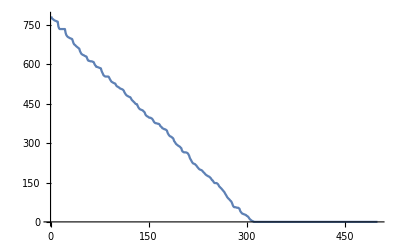

{{1,0.19133,0,0,900},{1,0.19133,0,2,896},{1,0.19133,0,1,832},{1,0.313105,0.0134549,0,792},{1,0.642172,0.004773,7,738},{1,0.642172,0.004773,0,704},{1,0.642172,0.004773,0,704},{1,0.642172,0.004773,3,702},{1,0.861716,0,3,700},{1,0.845845,0,2,700},{1,0.756908,0,0,694},{1,0.861716,0,1,694},{1,0.861716,0,0,694},{1,0.861716,0,0,694},{1,0.861716,0,1,694},{1,0.80194,0,2,694},{1,0.845845,0,0,694},{1,0.861716,0,0,694},{1,0.869757,0,0,694},{1,0.861716,0,0,694},{1,0.861716,0,1,694},{1,0.861716,0,3,694},{1,0.861716,0,0,694},{1,0.861716,0,1,692},{1,0.869757,0,3,688},{1,0.861716,0,1,688},{1,0.861716,0,2,688},{1,0.861716,0,4,688},{1,0.861716,0,1,688},{1,0.845845,0,3,688},{1,0.845845,0,4,688},{1,0.845845,0,2,688},{1,0.861564,0,3,688},{1,0.861716,0,2,688},{1,0.845845,0,2,688},{1,0.861716,0,4,688},{1,0.861716,0,2,688},{1,0.861716,0,3,688},{1,0.845845,0,3,688},{1,0.861716,0,2,688},{1,0.80194,0,5,688},{1,0.794607,0.0172665,2,688},{1,0.80194,0,2,682},{1,0.869757,0,2,682},{1,0.861716,0,2,682},{1,0.845845,0,2,682},{1,0.861716,0,1,682},{1,0.861716,0,6,682},{1,0.869757,0,5,682},{1,0.861716,0,4,682},{1,0.869757,0,0,682},{1,0.845845,0,2,682},{1,0.861716,0,5,682},{1,0.861716,0,2,682},{1,0.845845,0,1,682},{1,0.845845,0,3,682},{1,0.861716,0,0,682},{1,0.861716,0,3,682},{1,0.845845,0,2,682},{1,0.869757,0,6,676},{1,0.861716,0,2,676},{1,0.845845,0,3,676},{1,0.861716,0,4,676},{1,0.861716,0,2,676},{1,0.845845,0,2,676},{1,0.756908,0,6,676},{1,0.861716,0,7,676},{1,0.861564,0,2,676},{1,0.672749,0,6,674},{1,0.861716,0,3,670},{1,0.845845,0,10,670},{1,0.861716,0,3,670},{1,0.861716,0,4,670},{1,0.861716,0,4,670},{1,0.861716,0,6,670},{1,0.845845,0,4,664},{1,0.861716,0,10,664},{1,0.861716,0,4,664},{1,0.861716,0,9,660},{1,0.861716,0,10,660},{1,0.861716,0,9,660},{1,0.845845,0,6,658},{1,0.828696,0.0484392,9,658},{1,0.861716,0,8,654},{1,0.861716,0,10,654},{1,0.861716,0,10,654},{1,0.861716,0,10,654},{1,0.861716,0,7,654},{1,0.887212,0,10,654},{1,0.861716,0,10,654},{1,0.869757,0,10,654},{1,0.861716,0,9,654},{1,0.887212,0,8,654},{1,0.845845,0,7,652},{1,0.861716,0,10,648},{1,0.861716,0,10,648},{1,0.861716,0,10,648},{1,0.861716,0,10,648},{1,0.933779,0.0303896,10,648},{1,0.869757,0,10,642}}

```mathematica
RunSim[agentList_]:=Module[{agents=agentList,history={}},
For[k=1,k<300,k++,
{ag, ph} =DoRound[agents,800,500];
(*Print[Map[Function[a,Last[a]],ag]];*)
rankedAgents=Sort[ag,Last[#1]>Last[#2]&];
newAgents=Take[rankedAgents,Length[rankedAgents]/2];
newAgents=Join[newAgents,newAgents];
newAgents=Map[Function[a,{a[[1]],a[[2]],a[[3]],0,0}],newAgents];
(* Mutate agents *)
newAgents=Map[Function[a,If[RandomReal[]<0.05,MutateAgent[a],a]],newAgents];
agents=newAgents;
history=Append[history, ph];
];
{ag, ph} =DoRound[agents,800,500];
history=Append[history, ph];
{ag, history}
];

{a,h}=RunSim[agentParams];
ListLinePlot[h[[-1]]]
Sort[a,Last[#1]>Last[#2]&]
```

Simulation runs with agents mutating while pool is still functioning. Now if a lot of people donated in the past a new mutation can take advantage of this and vice versa.

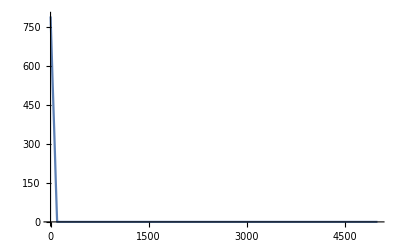

{{1,0.802099,0.111322,0,134},{1,0.814335,0.144492,0,134},{1,0.788725,0.158932,0,134},{1,0.809946,0.221409,0,134},{1,0.809946,0.221409,0,134},{1,0.809946,0.221409,0,134},{1,0.809946,0.221409,0,134},{1,0.809946,0.221409,0,134},{1,0.809946,0.221409,0,134},{1,0.809946,0.221409,0,134},{1,0.809946,0.221409,0,134},{1,0.809946,0.221409,0,134},{1,0.809946,0.221409,0,134},{1,0.809946,0.221409,0,134},{1,0.750279,0.262911,0,134},{1,0.750279,0.262911,0,134},{1,0.750279,0.262911,0,134},{1,0.765096,0.271274,0,134},{1,0.765096,0.271274,0,134},{1,0.765096,0.271274,0,134},{1,0.854708,0.285727,0,134},{1,0.896428,0.353975,0,134},{1,0.896428,0.353975,0,134},{1,0.896428,0.353975,0,134},{1,0.896428,0.353975,0,134},{1,0.896428,0.353975,0,134},{1,0.896428,0.353975,0,134},{1,0.896428,0.353975,0,134},{1,0.896428,0.353975,0,134},{1,0.896428,0.353975,0,134},{1,0.855922,0.402526,0,134},{1,0.858435,0.538807,0,134},{1,0.852395,0.630365,0,134},{1,0.852395,0.630365,0,134},{1,0.802099,0.111322,1,128},{1,0.829899,0.129582,1,128},{1,0.809946,0.221409,1,128},{1,0.809946,0.221409,1,128},{1,0.809946,0.221409,1,128},{1,0.809946,0.221409,1,128},{1,0.809946,0.221409,1,128},{1,0.809946,0.221409,1,128},{1,0.750279,0.262911,1,128},{1,0.750279,0.262911,1,128},{1,0.750279,0.262911,1,128},{1,0.750279,0.262911,1,128},{1,0.765096,0.271274,1,128},{1,0.765096,0.271274,1,128},{1,0.794276,0.282892,1,128},{1,0.896428,0.353975,1,128},{1,0.896428,0.353975,1,128},{1,0.896428,0.353975,1,128},{1,0.896428,0.353975,1,128},{1,0.858435,0.538807,1,128},{1,0.852395,0.630365,1,128},{1,0.802099,0.111322,2,122},{1,0.829899,0.129582,2,122},{1,0.829899,0.129582,2,122},{1,0.809946,0.221409,2,122},{1,0.809946,0.221409,2,122},{1,0.809946,0.221409,2,122},{1,0.809946,0.221409,2,122},{1,0.809946,0.221409,2,122},{1,0.750279,0.262911,2,122},{1,0.750279,0.262911,2,122},{1,0.750279,0.262911,2,122},{1,0.750279,0.262911,2,122},{1,0.765096,0.271274,2,122},{1,0.896428,0.353975,2,122},{1,0.852395,0.630365,2,122},{1,0.66872,0.0596285,3,116},{1,0.802099,0.111322,3,116},{1,0.809946,0.221409,3,116},{1,0.809946,0.221409,3,116},{1,0.750279,0.262911,3,116},{1,0.829899,0.129582,4,110},{1,0.788725,0.158932,4,110},{1,0.809946,0.221409,4,110},{1,0.809946,0.221409,4,110},{1,0.750279,0.262911,4,110},{1,0.858435,0.538807,4,110},{1,0.809946,0.221409,5,104},{1,0.750279,0.262911,5,104},{1,0.802099,0.111322,10,100},{1,0.802099,0.111322,10,100},{1,0.829899,0.129582,10,100},{1,0.809946,0.221409,10,100},{1,0.809946,0.221409,10,100},{1,0.809946,0.221409,10,100},{1,0.809946,0.221409,10,100},{1,0.962784,0.241126,10,100},{1,0.962784,0.241126,10,100},{1,0.794276,0.282892,10,100},{1,0.969757,0.304847,10,100},{1,0.896428,0.353975,10,100},{1,0.896428,0.353975,10,100},{1,0.896428,0.353975,10,100},{1,0.896428,0.353975,10,100},{1,0.858435,0.538807,10,100},{1,0.66872,0.0596285,8,86}}

```mathematica
RunSimContinuous[agentList_,initHealth_]:=Module[{agents=agentList,history={},poolHealth=initHealth},
For[k=1,k<50,k++,
{ag, ph} =DoRound[agents,poolHealth,100];
(*Print[Map[Function[a,Last[a]],ag]];*)
rankedAgents=Sort[ag,Last[#1]>Last[#2]&];
newAgents=Take[rankedAgents,Length[rankedAgents]/2];
newAgents=Join[newAgents,newAgents];
newAgents=Map[Function[a,{a[[1]],a[[2]],a[[3]],0,0}],newAgents];
(* Mutate agents *)
newAgents=Map[Function[a,If[RandomReal[]<0.05,MutateAgent[a],a]],newAgents];
agents=newAgents;
history=Join[history, ph];
poolHealth=ph[[-1]];
];
{ag, ph} =DoRound[agents,poolHealth,100];
history=Join[history, ph];
{ag, history}
];

{a,h}=RunSimContinuous[agentParams,8000];
ListLinePlot[Map[Function[x, x/fullToolHealth],h]](* plot the number of tools in the pool at any given time *)
Sort[a,Last[#1]>Last[#2]&]
```

In the above example we see a working pool where agents buy tools seldom and borrow more often. We also see that the pool is kept running by a few volunteers, everyone is not donating to the pool.